```mathematica
Quit[];
```

## KdV

```mathematica
iii[1,1]
```

iii[1,1]

```mathematica
ii[1,1]
```

ii[1,1]

```mathematica
θ[k_,x_,t_]:=2k x+8k^3t;
θx[k_,x_,t_]:=2k ;
Cs[x_,t_]:=Table[cs[[i]] Exp[I θ[ks[[i]],x,t]],{i,1,Length[ks]}];
θxs[x_,t_]:=Table[I*θx[ks[[i]],x,t],{i,1,Length[ks]}];
iii[x_,t_]:=(Abs[#]>10)&/@Cs[x//N,t//N];
ii[x_,t_]:=Module[{out={},out2={},data,j},
data = iii[x,t];
For[j=1,j≤Length[data],j++,
If[
data[[j]], AppendTo[out,j],AppendTo[out2,j]
];
];
{out,out2}
];
H [x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]] = -1/(ks[[i]]+ks[[j]]);
];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]] = 1/(ks[[i]]-ks[[j]]);
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]] = -1/(ks[[i]]+ks[[j]]);
];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]] = 1/(ks[[i]]-ks[[j]]);
];
];
h
];
q[k_,x_,t_,l_]:=Module[{out,is,isc,j},
{is,isc} = ii[x,t];
Product[
If[l≠is[[j]],(k-ks[[is[[j]]]])/(k+ks[[is[[j]]]]),1/(k+ks[[is[[j]]]])],
{j,1,Length[is]}]
]
diag[x_,t_]:=Module[{out=ConstantArray[0,Length[ks]],is,isc,i,Cexp,k},
{is,isc} = ii[x,t];
Cexp=Cs[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
out[[i]]=q[ks[[i]],x,t,i]^2*Cexp[[i]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
out[[i]]=1/(q[ks[[i]],x,t,i]^2*Cexp[[i]]);
];
out];
diagx[x_,t_]:=Module[{out=ConstantArray[0,Length[ks]],is,isc,i,Cexp,θprime,k},
{is,isc} = ii[x,t];
Cexp=Cs[x,t];
θprime=θxs[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
out[[i]]=q[ks[[i]],x,t,i]^2*Cexp[[i]]*θprime[[i]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
out[[i]]=1/(q[ks[[i]],x,t,i]^2*Cexp[[i]])(-θprime[[i]]);
];
out];
LS[x_,t_]:=Module[{A,b,diags,diagsx,Ax},
diags=diag[x,t];
diagsx=diagx[x,t];
A=IdentityMatrix[Length[ks]]-DiagonalMatrix[diags].H[x,t];
Ax=-DiagonalMatrix[diagsx].H[x,t];
{A,diags,Ax,diagsx}
];
WeightedSum[w_,x_,t_]:=Module[{is,isc,out=0,k,i},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
out = out + w[[i]]
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
out = out - w[[i]]
];
out];
qsol[x_,t_]:=Module[{A,b,Ax,bx,u,ux},
{A,b,Ax,bx}=LS[x,t];
u=LinearSolve[A,b]//Quiet;
ux = LinearSolve[A,bx-Ax.u]//Quiet;
2I WeightedSum[ux,x,t]
];
```

```mathematica
diag[0,0]//N
```

### Floating point

```mathematica
ks =I*Table[.05*i,{i,1,20}]
cs = ks;
```

{0.+0.05 ⅈ,0.+0.1 ⅈ,0.+0.15 ⅈ,0.+0.2 ⅈ,0.+0.25 ⅈ,0.+0.3 ⅈ,0.+0.35 ⅈ,0.+0.4 ⅈ,0.+0.45 ⅈ,0.+0.5 ⅈ,0.+0.55 ⅈ,0.+0.6 ⅈ,0.+0.65 ⅈ,0.+0.7 ⅈ,0.+0.75 ⅈ,0.+0.8 ⅈ,0.+0.85 ⅈ,0.+0.9 ⅈ,0.+0.95 ⅈ,0.+1. ⅈ}

```mathematica
dt=.4;frames=ParallelTable[DiscretePlot[qsol[xx,i*dt],{xx,-40,80,.1},Joined->True,PlotRange->{All,{0,2}},Axes->False,Frame->True],{i,1,100}];
ListAnimate[frames]
```

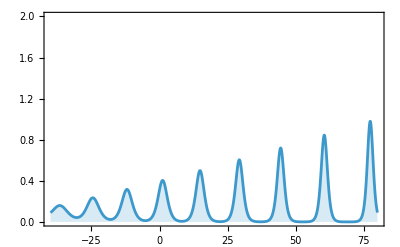

```mathematica
DiscretePlot[qsol[xx,50.0],{xx,-40,80,.1},Joined->True,PlotRange->{All,{0,2}},Axes->False,Frame->True]
```

```mathematica
t = 10dt
```

```mathematica
Cs[-5,4]
```

```mathematica
diag[-5,4]
```

```mathematica
frames[[10]]
```

```mathematica
Export["~/solitons.gif",frames]
```

### High-precision

```mathematica
sp[x_]:=SetPrecision[x,300];
```

```mathematica
ks =I*Table[i/50,{i,1,50}]//sp;
cs=ks;
x =0//sp;t=0//sp;
```

```mathematica
cs//N
```

```mathematica
diag[0,0]//N
```

```mathematica
qsol[x,t]
```

```mathematica
Monitor[DiscretePlot[qsol[xx,t],{xx,-80,80,1/10},Joined->True,PlotRange->{All,{0,2}},Axes->False,Frame->True],xx//N]
```

## Focusing NLS

```mathematica
(*θ[k_,x_,t_]:=2k x+4k^2t;*)
θ[k_,x_,t_]:=2k x+2k^2t;
cc[x_]:=Conjugate[x];
Cs[x_,t_]:=Table[cs[[i]] Exp[I θ[ks[[i]],x,t]],{i,1,Length[ks]}];
iii[x_,t_]:=(Abs[#]>1)&/@Cs[x//N,t//N];
ii[x_,t_]:=Module[{out={},out2={},data,j},
data = iii[x,t];
For[j=1,j≤Length[data],j++,
If[
data[[j]], AppendTo[out,j],AppendTo[out2,j]
];
];
{out,out2}
];
H11[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]]);
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]]);
];
];
h
];
H22[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]])//cc;
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]])//cc;
];
];
h
];
H12[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(ks[[i]]-cc[ks[[j]]]);
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(ks[[i]]-cc[ks[[j]]]);
];
];
h
];
H21[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(cc[ks[[i]]]-ks[[j]]);
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(cc[ks[[i]]]-ks[[j]]);
];
];
h
];
q[k_,x_,t_]:=Module[{out,is,isc,j},
{is,isc} = ii[x,t];
Product[(k-ks[[is[[j]]]])/(k-cc[ks[[is[[j]]]]]),
{j,1,Length[is]}]
];
quhp[k_,x_,t_,l_]:=Module[{out,is,isc,j},
{is,isc} = ii[x,t];
Product[
If[l≠is[[j]],(k-ks[[is[[j]]]])/(k-cc[ks[[is[[j]]]]]),1/(k-cc[ks[[is[[j]]]]])],
{j,1,Length[is]}]
];
qlhp[k_,x_,t_,l_]:=Module[{out,is,isc,j},
{is,isc} = ii[x,t];
Product[
If[l≠is[[j]],(k-ks[[is[[j]]]])/(k-cc[ks[[is[[j]]]]]),(k-ks[[is[[j]]]])],
{j,1,Length[is]}]
];
diag1[x_,t_]:=Module[{out=ConstantArray[0,Length[ks]],is,isc,i,Cexp,k},
{is,isc} = ii[x,t];
Cexp=Cs[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
out[[i]]=q[ks[[i]],x,t]^2*Cexp[[i]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
out[[i]]=1/(quhp[ks[[i]],x,t,i]^(2)*Cexp[[i]]);
];
out];
diag2[x_,t_]:=Module[{out=ConstantArray[0,Length[ks]],is,isc,i,Cexp,k},
{is,isc} = ii[x,t];
Cexp=Cs[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
out[[i]]=-q[ks[[i]]//cc,x,t]^(-2)*cc[Cexp[[i]]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
out[[i]]=-qlhp[ks[[i]]//cc,x,t,i]^(2)/(cc[Cexp[[i]]]);
];
out];
LS[x_,t_]:=Module[{A,b,diags1,diags2,Ax,b1,b2,is,isc,k,i,H},
diags1=diag1[x,t];
diags2=diag2[x,t];
(*b1 = ConstantArray[0,Length[ks]];b2=b1;
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
b2[[i]]=diags2[[i]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
b1[[i]]=diags1[[i]];
];
b = Join[b1,b2];*)

b1 = ConstantArray[0,Length[ks]];b2=b1;
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
b2[[i]]=1;
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
b1[[i]]=1;
];
b = Join[b1,b2];

H=Join[Join[H11[x,t],H12[x,t],2],Join[H21[x,t],H22[x,t],2]];
A=IdentityMatrix[2Length[ks]]-DiagonalMatrix[Join[diags1,diags2]].H;
{A,DiagonalMatrix[Join[diags1,diags2]].b}
];
sol[x_,t_]:=Module[{A,b,Ax,bx,u,ux,u1,u2,sum,k,i,isc,is},
{A,b}=LS[x,t];
u=LinearSolve[A,b];
u2=u[[Length[ks]+1;;]];
u1=u[[1;;Length[ks]]];
sum = 0;
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
sum = sum + u2[[i]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
sum = sum + u1[[i]];
];
2I sum
];
```

### Floating point

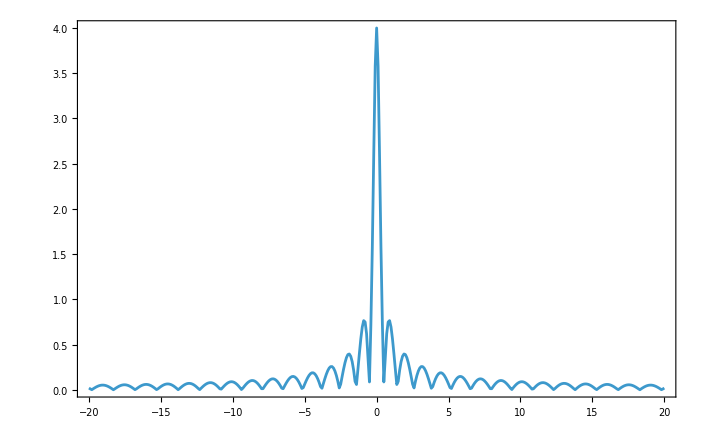

C:\Users\MazzucaGuido\Documents\Wolfram\50solitonPIII.csv

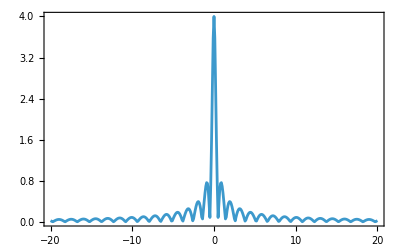

```mathematica
Nsoliton=50;
ks=Table[1*i+I,{i,1,Nsoliton}];
μD=1;
Nmax=Nsoliton;
norming[n_]:=Module[{ln=ks[[n]]},prod1=Product[ln-Conjugate[ks[[ell]]],{ell,1,Nmax}];
prod2=Times@@(1/(ln-#)&/@Delete[ks,n]);
prod1*prod2]
cs=Table[norming[n],{n,1,Nsoliton}];
data=ParallelTable[{xx,Abs[2/(Nsoliton μD)sol[(2 xx)/(Nsoliton μD),0]]},{xx,-20,20,.1}];
ListPlot[data,Joined->True,PlotRange->All,Axes->False,Frame->True]
path=FileNameJoin[{NotebookDirectory[],"50solitonPIII.csv"}];
Export[path,data];
path
```

```mathematica
path=FileNameJoin[{NotebookDirectory[],"50solitonPIII.csv"}];
Export[path,data];
path
```

C:\Users\GKOGKOUAIKATERINI\Desktop\max\50solitonPIII.csv

### Floating point

```mathematica
ks =Table[I+i,{i,-5,5,1}]//sp;
cs=I Im[ks];
```

```mathematica
dt=.4;data=Table[Table[{xx,sol[xx,i*dt]},{xx,-40,40,.1}],{i,1,10}];
```

```mathematica
Table[ListPlot[data[[i]]//Re,Joined->True,PlotRange->{All,{-2,2}},Axes->False,Frame->True],{i,1,Length[data]}]//ListAnimate
```

### High-precision

```mathematica
sp[x_]:=SetPrecision[x,300];
```

```mathematica
ks =Table[I+i,{i,-10,10,1}]//sp;
cs=I Im[ks];
x =1//sp;t=1//sp;
h = 1/1000000000000//sp;
sol[x,t]
I(sol[x,t+h]-sol[x,t-h])/(2h) +(sol[x+h,t]-2sol[x,t]+sol[x-h,t])/h^2+2 Abs[sol[x,t]]^2sol[x,t]//N
```